```mathematica
<<"/home/naxicon/Apps/MathematicaScripts/Dynamica.m"
```

Dynamica (Version 1.0.11 - 5/8/2021), Copyright(c) 1993-2021 Randall D. Beer. All rights reserved.

THIS SOFTWARE IS DISTRIBUTED 'AS IS'. NO WARRANTY OF ANY KIND IS EXPRESSED OR IMPLIED.

1

1

3.1

DynamicalSystem[«3 ODEs»,{f,p,r},{we→18,wi→10}]

DynamicalSystem[«3 ODEs»,{f,p,r},{we→18,wi→3}]

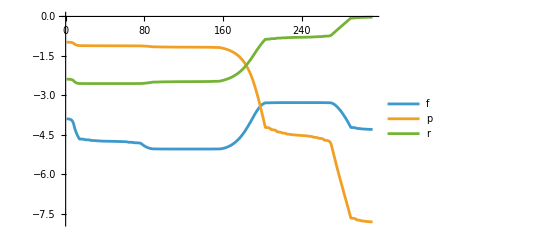

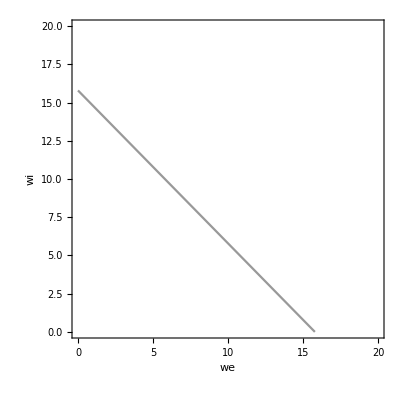

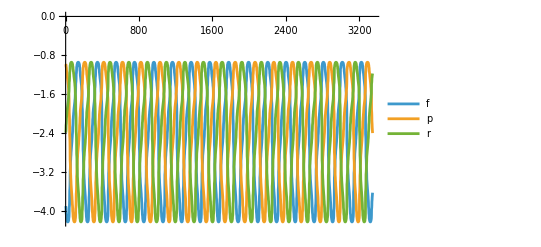

```mathematica
ws = 1
mult=1
df =-f +(ws) LogisticSigmoid[f] - (mult we) LogisticSigmoid[p]-(mult wi)*LogisticSigmoid[r];
dp =-p +(ws) LogisticSigmoid[p] - (mult we) LogisticSigmoid[r]-(mult wi)*LogisticSigmoid[f];
dr =-r +(ws) LogisticSigmoid[r] - (mult we) LogisticSigmoid[f]-(mult wi)*LogisticSigmoid[p];
min = -7.1;
max = 3.1
ctrnn = DynamicalSystem[{df,dp,dr},{{f,min,max},{p,min,max},{r,min,max}},{{we,0,20},{wi,0,20}}];
ds1 = ctrnn/.{we->18,wi->10}
ds2 =ctrnn/.{we->18,wi->3}
DisplayTrajectories[ds1,{{-3.891110283314832,-0.977568554821239,-2.383956967098818}}, 100];
tp = Transpose[$Trajectories[[1]]];
t1 = tp[[1]];
t2 = tp[[2]];
t3 = tp[[3]];
ListPlot[{t1,t2,t3},Joined->True,PlotLegends->{"f","p","r"}]
DisplayTrajectories[ds2,{{-3.891110283314832,-0.977568554821239,-2.383956967098818}}, 100];
DisplayParameterChart[ctrnn,{we,wi}]
tp = Transpose[$Trajectories[[1]]];
t1 = tp[[1]];
t2 = tp[[2]];
t3 = tp[[3]];
ListPlot[{t1,t2,t3},Joined->True,PlotLegends->{"f","p","r"}]
```

```mathematica
DisplayTrajectories[ds2,{{0.5,0.1,0.1}},100]
DisplayPhasePortrait[ds2, Tries->500]
```

-Graphics3D-

-Graphics3D-

```mathematica
Last[$Trajectories[[1]]]
```

{-3.89111,-0.977569,-2.38396}

10.1

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {f,p,wi,ws}={2.24213900960455,2.24213900960455,4.51967624955033,7}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {f,p,wi,ws}={-1.27846454276107,-1.27846454276107,5.8695860194297,0}

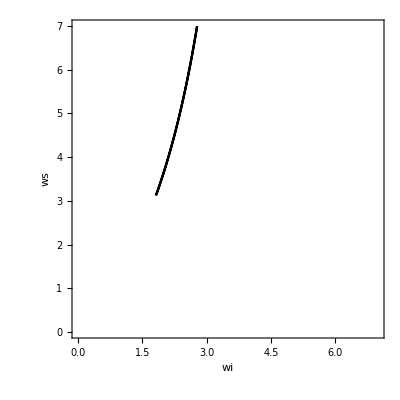

```mathematica
df =-f +ws LogisticSigmoid[f] - (wi) LogisticSigmoid[p];
dp =-p +ws LogisticSigmoid[p] - (wi) LogisticSigmoid[f];
min = -10.1;
max = 10.10
ctrnn = DynamicalSystem[{df,dp},{{f,min,max},{p,min,max}},{{wi,0,7},{ws,0,7}}];
DisplayParameterChart[ctrnn,{wi,ws}, Tries->1000]
```

```mathematica
DisplayBifurcationDiagram[ctrnn/.{wi->8},we, StateVariables->{r,p}]
```

-Graphics3D-

-Graphics3D-

```mathematica
$BifurcationDiagramBPs
```

{BifurcationPoint[Fold,{-0.139260670024354,-4.06315981482147,-2.68810222216857},{we→5.62407397729453,wi→8}],BifurcationPoint[Fold,{-4.06315981482147,-2.68810222216857,-0.139260670024354},{we→5.62407397729453,wi→8}],BifurcationPoint[Fold,{-2.68810222216857,-0.139260670024354,-4.06315981482147},{we→5.62407397729453,wi→8}],BifurcationPoint[Hopf,{-1.90918491668036,-1.90918491668036,-1.90918491668036},{we→7.79157568956269,wi→8}]}

```mathematica
gc1 =ctrnn /.{we->.8, wi->.2}
time = 1000
DisplayFlow[gc1,20, FlowPlotMode->Boundary]
DisplayPhasePortrait[gc1, Tries->200, SaddleManifolds->True]
```

DynamicalSystem[«3 ODEs»,{f,p,r},{we→0.8,wi→0.2}]

1000

-Graphics3D-

-Graphics3D-

```mathematica
DisplayPhasePortrait[gc1, Tries->200, SaddleManifolds->True]
$PhasePortraitEPs
```

-Graphics3D-

{EquilibriumPoint[Saddle,Mixed,{-1.56123,-1.56123,-1.56123}]}

```mathematica
Manipulate[DisplayPhasePortrait[ctrnn/.{we->a,wi->-4}],{a,-10,5}]
```

-Graphics3D-

```mathematica
DisplayFlow[gc1,time, FlowPlotMode->Boundary]
DisplayTrajectories[gc1,{{10,0.1,0.1}},time, PlotPoints->time * 10];
```

-Graphics3D-

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {f,p,r,α,β}={1.,0,0,0,1.}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {f,p,r,α,β}={0,-1.,0,0,1.}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {f,p,r,α,β}={0,0,-1.,0,1.}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {f,p,r,α,β}={0,0,1.,0,1.}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {f,p,r,α,β}={0,1.,0,0,1.}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {f,p,r,α,β}={-1.,0,0,1.,3}

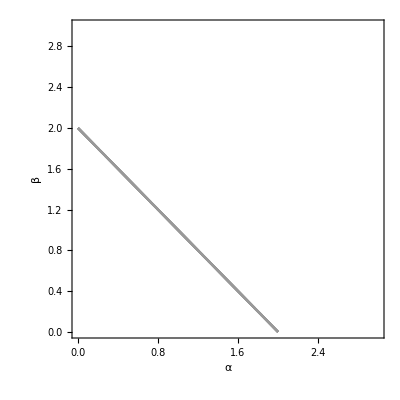

```mathematica
DisplayParameterChart[glv,{α,β}]
```

```mathematica
DisplayBifurcationDiagram[glv/.{α->2.1},β,StateVariables->{f,r}]
```

-Graphics3D-

```mathematica
$BifurcationDiagramBPs
```

{BifurcationPoint[Branch,{-1.,0,0},{α→2.1,β→1.}],BifurcationPoint[Branch,{0,-1.,0},{α→2.1,β→1.}],BifurcationPoint[Branch,{0,0,-1.},{α→2.1,β→1.}],BifurcationPoint[Branch,{0,0,1.},{α→2.1,β→1.}],BifurcationPoint[Branch,{0,1.,0},{α→2.1,β→1.}],BifurcationPoint[Branch,{1.,0,0},{α→2.1,β→1.}]}

```mathematica
how to continue a bifurcation julia
```

```mathematica
FollowBifurcationBranch[]
```